```mathematica
f[x_]:=Sin[6 x]^3-Cos[5*E^x];
ff[x_]:=-Sin[6x]^3-Cos[5 E^x];
```

```mathematica
D[f[x],{x,3}]
```

75 ⅇ^(2 x) Cos[5 ⅇ^x]+1296 Cos[6 x]^3+5 ⅇ^x Sin[5 ⅇ^x]-125 ⅇ^(3 x) Sin[5 ⅇ^x]-4536 Cos[6 x] Sin[6 x]^2

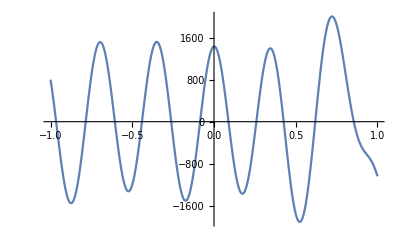

```mathematica
Plot[75 ⅇ^(2 x) Cos[5 ⅇ^x]+1296 Cos[6 x]^3+5 ⅇ^x Sin[5 ⅇ^x]-125 ⅇ^(3 x) Sin[5 ⅇ^x]-4536 Cos[6 x] Sin[6 x]^2,{x,-1,1}]
```

```mathematica
D[ff[x],{x,3}]
```

75 ⅇ^(2 x) Cos[5 ⅇ^x]-1296 Cos[6 x]^3+5 ⅇ^x Sin[5 ⅇ^x]-125 ⅇ^(3 x) Sin[5 ⅇ^x]+4536 Cos[6 x] Sin[6 x]^2

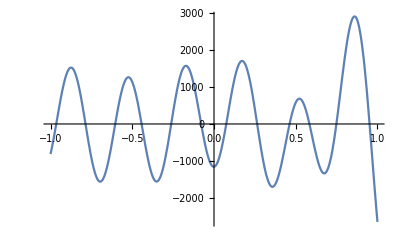

```mathematica
Plot[75 ⅇ^(2 x) Cos[5 ⅇ^x]-1296 Cos[6 x]^3+5 ⅇ^x Sin[5 ⅇ^x]-125 ⅇ^(3 x) Sin[5 ⅇ^x]+4536 Cos[6 x] Sin[6 x]^2,{x,-1,1}]
```

```mathematica
G[x_]:=If[Sin[6 x]≥0,D[f[x],{x,4}],D[ff[x],{x,4}]];
```

```mathematica
NIntegrate[Abs[G[x]],{x,-1,1}]
```

37684.